```mathematica
rhoa = Flatten[Import["/Users/deboramroczek/Desktop/MSU_2019/acceptable_rho.dat"]];
wa = Flatten[Import["/Users/deboramroczek/Desktop/MSU_2019/acceptable_w.dat"]];
rhop = Flatten[Import["/Users/deboramroczek/Desktop/MSU_2019/pathological_rho.dat"]];
wp = Flatten[Import["/Users/deboramroczek/Desktop/MSU_2019/pathological_w.dat"]];
```

```mathematica
path=Transpose@{wp,rhop};
acc=Transpose@{wa,rhoa};
```

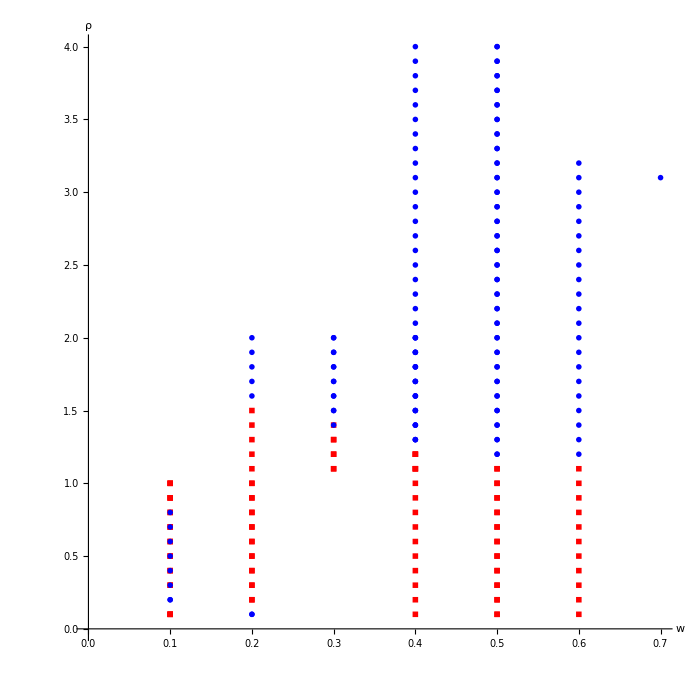

```mathematica
ListPlot[{path,acc}, Joined-> False, PlotMarkers->{■,●},PlotStyle-> {Directive[Red,PointSize[Medium]],Directive[Blue,PointSize[Medium]]},ImageSize->700,AxesStyle->Directive[Black, 25],AxesLabel-> {"w","ρ"},AspectRatio->1]
```